## Ref: https://arxiv.org/pdf/0706.2210.pdf

#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];
LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

```mathematica
NotebookDirectory[]//SetDirectory;
<<"./7o/7o_master_file.m"
```

```mathematica
ReadInDMFile[DensityMatrixFile_]:=Block[{},
inputstring=Import[DensityMatrixFile,"TSV"];
DensityMatrixVector={};
For[i=1,i<=Length[inputstring],i++,
JT=StringCases[inputstring[[i,1]],RegularExpression["ONE.+JO.+\\s(\\d+)\\s.+(\\d+).*"]->{"$1","$2"}]//ToExpression;
dens=StringCases[inputstring[[i,1]],RegularExpression["(\\d+)\\s+(\\d+)\\s+(\\d+)\\s+(\\d+)\\s+(.+\\d+.\\d+).+"]->{"$1","$2","$3","$4","$5"}]//ToExpression;
If[{}!=JT,oJT=JT[[1]]/2;];
If[{}!=dens,oDens={dens[[1,5]],{dens[[1,1]],dens[[1,2]]/2},{dens[[1,3]],dens[[1,4]]/2},oJT[[1]],oJT[[2]]};DensityMatrixVector=DensityMatrixVector~Join~{oDens}];];

For[i=1,i<=Length[DensityMatrixVector],i++,
DensityMatrix[i]=DensityMatrixVector[[i]];];
SetDMmatrixLength[Length[DensityMatrixVector]];
Return[];];
```

All energy is in GeV

### Constant

```mathematica
(* symbol, Z, A, Spin at ground state, density matrices file path*)
Ar40={"Ar",18,40,0,"./ar40_obdm9.dat"};
ΔE=3.259 10^-3;
SpinJ=1;
OutputNameEr="pointsEr/NC1.csv";
OutputNameNC="pointsNC/NC1.csv";
antineu=1; (*-1 for ν-bar, +1 for ν*)

evenJ=EvenQ[SpinJ];
If[SpinJ==0,J0=0,J0=1];
```

```mathematica
Nucleus=Ar40;
mN=0.938;
mA=Nucleus⟦3⟧ mN;
Ji=Nucleus⟦4⟧;
me=0.5110 10^-3;
mπ=0.139;
mμ=0.1056;
GF=1.166 10^-5;
Subscript[g, A]=1.258;
Subscript[M, A]=1.05;
F1=1;
FA=-Subscript[g, A];
FP=(2 mN FA)/(mπ^2-q^2);
μ1=4.706;
GeVcm=(6.5821 10^-25) (3 10^10);
sinΘc=0.22;
sin2Θw=0.2229;
cosΘc=√(1-sinΘc^2);
ℏ𝒸=0.197;
alpha=1/137;
qVp=0.01556533;
qVn=-0.5122125;
b[A_]:=√(41.467/(45 A^(-1/3)-25 A^(-2/3)));
yy[q_,A_]:= ((q b[A])/(2ℏ𝒸))^2;
```

### Read density matrix file

```mathematica
NotebookDirectory[]//SetDirectory;
ReadInDMFile[Nucleus⟦5⟧];
```

```mathematica
ΨJ2T0=Select[DensityMatrixVector,(#[[5]]==0)&];
ΨJ2T1=Select[DensityMatrixVector,(#[[5]]==1)&];
```

```mathematica
ThreeJSymbol[{2,-2},{0,0},{2,2}]
ThreeJSymbol[{2,-2},{1,0},{2,2}]
```

1/(√5)

√(2/15)

```mathematica
ΨJ2T0[[All,1]]=ΨJ2T0[[All,1]]/√5;
ΨJ2T1[[All,1]]=ΨJ2T1[[All,1]] √(2/15);
```

### Multipole Operator

```mathematica
M[y_,{Np_,jp_},{N_,j_},J_]:=F1 MJ[y,{Np,jp},{N,j},J];
M5[y_,{Np_,jp_},{N_,j_},J_]:=(I q)/mN (FA  OmegaPJ[y,{Np,jp},{N,j},J]+(ω FP)/2 SigmaPPJ[y,{Np,jp},{N,j},J]);
L[y_,{Np_,jp_},{N_,j_},J_]:=ω/q M[y,{Np,jp},{N,j},J]J0;
L5[y_,{Np_,jp_},{N_,j_},J_]:=I (FA - q^2/(2mN)FP)SigmaPPJ[y,{Np,jp},{N,j},J] ;
Subscript[T, el][y_,{Np_,jp_},{N_,j_},J_]:=q/mN( F1 DeltaPJ[y,{Np,jp},{N,j},J]+1/2 μ1 SigmaJ[y,{Np,jp},{N,j},J])J0;
Subscript[T, el5][y_,{Np_,jp_},{N_,j_},J_]:=I FA SigmaPJ[y,{Np,jp},{N,j},J];
Subscript[T, mag][y_,{Np_,jp_},{N_,j_},J_]:=-(I q)/mN(F1 DeltaJ[y,{Np,jp},{N,j},J]-μ1/2 SigmaPJ[y,{Np,jp},{N,j},J]);
Subscript[T, mag5][y_,{Np_,jp_},{N_,j_},J_]:=FA SigmaJ[y,{Np,jp},{N,j},J]J0;
```

```mathematica
SummedM[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*M[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
SummedM5[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*M5[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
SummedL[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*L[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
SummedL5[y_,Ψi_]:=Sum[Ψi⟦i,1⟧*L5[y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, el][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, el][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, el5][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, el5][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, mag][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, mag][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
Subscript[SummedT, mag5][y_,Ψi_]:=Sum[Ψi⟦i,1⟧*Subscript[T, mag5][y,Ψi[[i,2]],Ψi[[i,3]],Ψi[[i,4]]],{i,1,Length[Ψi]}];
```

Calculate the three terms governing the nuclear response (see Eq. (33)), removing the common term e^(-2y).

```mathematica
ΨJ2T=ΨJ2T0;
```

```mathematica
FirstTerm[y_]:=Simplify[Exp[2 y](SummedM[y,ΨJ2T]+ω/q SummedL[y,ΨJ2T])Conjugate[(SummedM[y,ΨJ2T]+ω/q SummedL[y,ΨJ2T])],{q,ω,y}∈ Reals];
FirstTerm5[y_]:=Simplify[Exp[2 y](SummedM5[y,ΨJ2T]+ω/q SummedL5[y,ΨJ2T])Conjugate[(SummedM5[y,ΨJ2T]+ω/q SummedL5[y,ΨJ2T])],{q,ω,y}∈ Reals];
SecondTerm[y_]:=Simplify[Exp[2 y](Subscript[SummedT, el][y,ΨJ2T]Conjugate[Subscript[SummedT, el][y,ΨJ2T]]+Subscript[SummedT, mag5][y,ΨJ2T]Conjugate[Subscript[SummedT, mag5][y,ΨJ2T]]),{q,ω,y}∈ Reals];
SecondTerm5[y_]:=Simplify[Exp[2 y](Subscript[SummedT, el5][y,ΨJ2T]Conjugate[Subscript[SummedT, el5][y,ΨJ2T]]+Subscript[SummedT, mag][y,ΨJ2T]Conjugate[Subscript[SummedT, mag][y,ΨJ2T]]),{q,ω,y}∈ Reals];
Tel5Term[y_]:=Simplify[Exp[2 y](Subscript[SummedT, el5][y,ΨJ2T]Conjugate[Subscript[SummedT, el5][y,ΨJ2T]]),{q,ω,y}∈ Reals];
ThirdTerm[y_]:=Simplify[Exp[2 y]Re[Subscript[SummedT, mag5][y,ΨJ2T]  Conjugate[Subscript[SummedT, el][y,ΨJ2T]]],{q,ω,y}∈ Reals];
ThirdTerm5[y_]:=Simplify[Exp[2 y]Re[Subscript[SummedT, mag][y,ΨJ2T]  Conjugate[Subscript[SummedT, el5][y,ΨJ2T]]],{q,ω,y}∈ Reals];
```

```mathematica
XsectionNC0[ϵ_,y_]:=(2 ϵ^2)/(π(2Ji+1))GF^2  Cos[θ/2]^2 Exp[-2 y](FirstTerm[y]+  (-qμ2/(2 q^2) + Tan[θ/2]^2)SecondTerm[y] - 2 antineu Tan[θ/2] √(-qμ2/q^2 + Tan[θ/2]^2)ThirdTerm[y])/.qμ2->ω^2-q^2;
XsectionNC5[ϵ_,y_]:=(2 ϵ^2)/(π(2Ji+1))GF^2  Cos[θ/2]^2 Exp[-2 y](FirstTerm5[y]+  (-qμ2/(2 q^2) + Tan[θ/2]^2)SecondTerm5[y] - 2 antineu Tan[θ/2] √(-qμ2/q^2 + Tan[θ/2]^2)ThirdTerm5[y])/.qμ2->ω^2-q^2;
```

### |cosθ|<1 constraint

```mathematica
ErTolerance=.005;(*to avoid numerical error and imaginary number*)
ErMax[Enu_]:=(4 Enu^2-4Enu ΔE+ΔE^2)/(2(Enu+mA)) (1-ErTolerance);
ErMin=(mA-√(mA (mA-2 ΔE))-ΔE)(1+ErTolerance);
```

```mathematica
dcosθdEr[Enu_]:=mA/(Enu (Enu-ΔE));
```

### Cross section

```mathematica
XsectionNC[ϵ_,y_]:=If[evenJ,XsectionNC0[ϵ,y],XsectionNC5[ϵ,y]];
```

```mathematica
dσdErInelasticNC[ER_,Eν_]:=XsectionNC[Eν-ΔE-ER,yy[q,Nucleus⟦3⟧]]2π dcosθdEr[Eν]/.{ω->(ΔE+ER)*0,θ->ArcCos[(ER^2+2 Eν^2-2Eν ΔE-2Eν ER-2mA ER+ΔE^2+2ER ΔE)/(2Eν(Eν-ΔE-ER))],q->√(2mA ER)};
```

```mathematica
σInelasticNC[Enu_]:=If[Enu>ΔE, NIntegrate[dσdErInelasticNC[ER,Enu],{ER,ErMin,ErMax[Enu]}],0];
```

```mathematica
FHelm[A_,Er_]:=3(Sin[q r]-(q r)Cos[q r])/(q r)^3 Exp[(-(q s)^2)/2]/.{q->6.92*10^-3 √A √Er,r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9}
dσdErHi[ErkeV_,EnuMeV_]:=(GF^2(Nucleus⟦3⟧ mN))/(2π)(1+(1-ErkeV/(EnuMeV 10^3))^2-(Nucleus⟦3⟧ mN ErkeV)/EnuMeV^2)(Nucleus⟦2⟧ qVp+(Nucleus⟦3⟧-Nucleus⟦2⟧) qVn)^2 FHelm[Nucleus⟦3⟧,ErkeV]^2;
```

### Plot

```mathematica
pointsEl=Table[10^-6 10^42 GeVcm^2 NIntegrate[dσdErHi[Er,EnuMeV],{Er,0,(2 EnuMeV^2 10^6)/(mA 10^6+2 10^3 EnuMeV)}],{EnuMeV,1,100}];
pointsNC=Table[{EnuMeV,10^42 GeVcm^2 σInelasticNC[EnuMeV 10^-3]},{EnuMeV,Range[1,100,2]}];
(*Export[OutputNameNC,pointsNC];*)
```

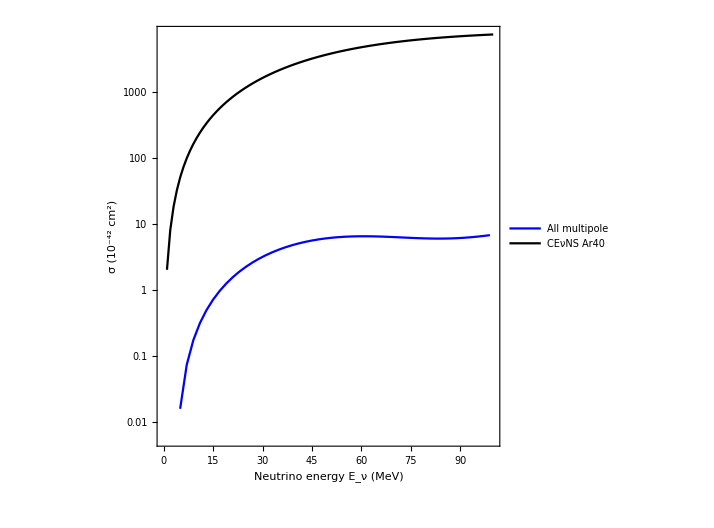

```mathematica
ListLogPlot[{pointsNC,pointsEl},Joined->True,PlotStyle->{Blue,Black},PlotLegends->Legend[{"All multipole","CEνNS Ar40"},Position->{0.75,0.2},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Black]&)],FrameLabel->{"Neutrino energy E_ν (MeV)", "σ (10^-42 cm^2)"}]
```